```mathematica
SetDirectory[NotebookDirectory[]];
ClearAll["Global`*"]
```

## Bernoulli example (not used - see Normal one below)

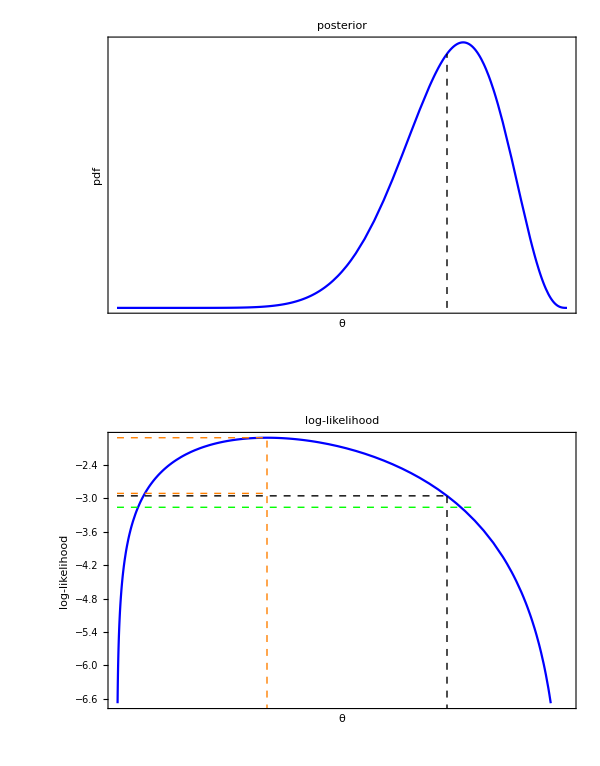

```mathematica
{α,β} = {10,2};
n =3;
data = RandomVariate[BernoulliDistribution[0.5],n];
aTrueDist =BernoulliDistribution[0.5];
(*data = {1,0,1};*)
gPrior = Plot[PDF[BetaDistribution[α,β],x],{x,0,1},Frame->{True,True,False,False},FrameTicks->{None,None},PlotStyle->Blue,FrameLabel->{"θ","pdf"},BaseStyle->{FontSize->14},PlotLabel->"prior"];
aPosteriorDist = BetaDistribution[α+Total@data,β +n - Total@data];
aMLE=NSolve[D[LogLikelihood[BernoulliDistribution[θ],data],θ]==0,θ,Reals][[1,1,2]];
aBayesPoint=Mean@aPosteriorDist;
aBayesFull = N@Expectation[LogLikelihood[BernoulliDistribution[θ],data],θ\[Distributed]aPosteriorDist];
gPosterior = Plot[{PDF[aPosteriorDist,x] },{x,0,1},Frame->{True,True,False,False},FrameTicks->{None,None},PlotStyle->Blue,FrameLabel->{"θ","pdf\n\n"},BaseStyle->{FontSize->14},Epilog->{Dashed,Line[{{aBayesPoint,0},{aBayesPoint,PDF[aPosteriorDist,aBayesPoint]}}]},PlotLabel->"posterior"];
gLogLikelihood = Plot[LogLikelihood[BernoulliDistribution[θ],data],{θ,0,1},Epilog->{{Orange,Dashed,Line[{{0,LogLikelihood[BernoulliDistribution[aMLE],data]},{aMLE,LogLikelihood[BernoulliDistribution[aMLE],data]}}],Line[{{aMLE,-100},{aMLE,LogLikelihood[BernoulliDistribution[aMLE],data]}}],Line[{{0,LogLikelihood[BernoulliDistribution[aMLE],data]-1},{aMLE,LogLikelihood[BernoulliDistribution[aMLE],data]-1}}]},{Black,Dashed,Line[{{aBayesPoint,-100},{aBayesPoint,LogLikelihood[BernoulliDistribution[aBayesPoint],data]}}],Line[{{0,LogLikelihood[BernoulliDistribution[aBayesPoint],data]},{aBayesPoint,LogLikelihood[BernoulliDistribution[aBayesPoint],data]}}]},{Green,Dashed,Line[{{0,aBayesFull},{0.8,aBayesFull}}]}},Frame->{True,True,False,False},FrameTicks->{None,True},PlotStyle->Blue,FrameLabel->{"θ","log-likelihood"},BaseStyle->{FontSize->14},PlotLabel->"log-likelihood"];
Show[GraphicsColumn[{gPosterior,gLogLikelihood}],ImageSize->600]
```

```mathematica
lppd=N@Log@Expectation[Likelihood[BernoulliDistribution[θ],data],θ\[Distributed]aPosteriorDist]
```

-2.92022

```mathematica
elppdTrue=n*Expectation[Log@Simplify[Expectation[Likelihood[BernoulliDistribution[θ],{y}],θ\[Distributed]aPosteriorDist],0≤ y≤ 1],y\[Distributed]aTrueDist]
```

-2.44787

```mathematica
elppdAIC = LogLikelihood[BernoulliDistribution[aMLE],data]-1
```

-2.90954

```mathematica
elppdDIC = LogLikelihood[BernoulliDistribution[aBayesPoint],data] - 2(LogLikelihood[BernoulliDistribution[aBayesPoint],data]- aBayesFull)
```

-3.36444

```mathematica
elppdWAIC = lppd - 2(lppd-aBayesFull)
```

-3.39788

## Normal example (this is the one that is used)

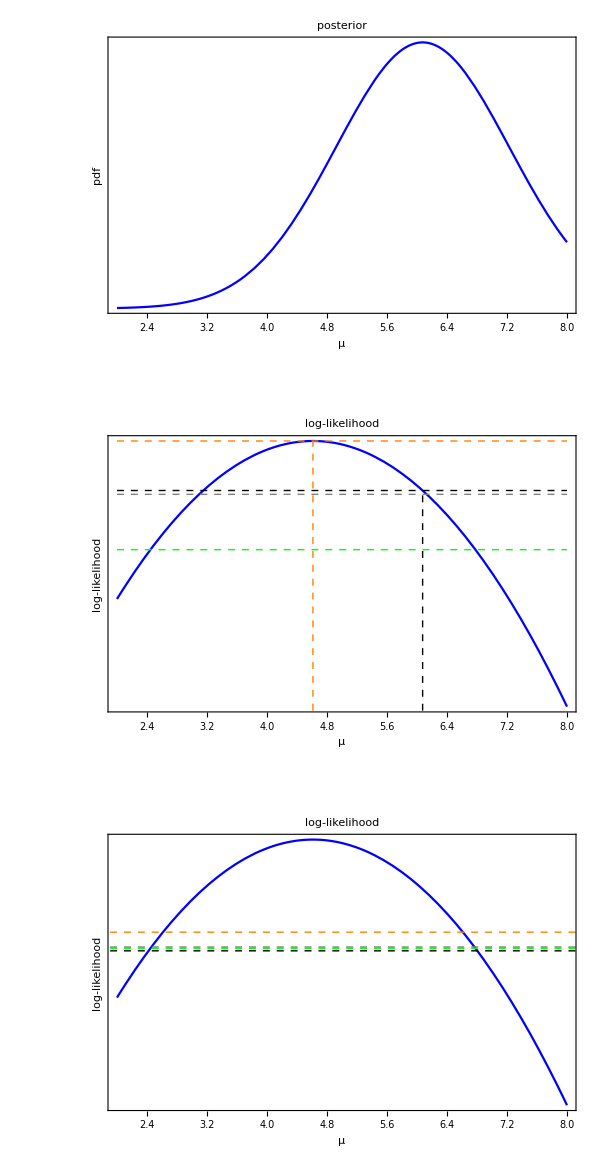

```mathematica
trueDist = NormalDistribution[5,2];
n = 2;
(*data = RandomVariate[trueDist,n];*)
data = {5.180800850439462,4.044156763676277};
xbar = Mean@data;
μ0 = 9;
σ0 = 2;
σ1 = 2;
aPosteriorDist = NormalDistribution[((μ0/(σ0^2)) + (n xbar)/(σ1^2)) / ((1/(σ0^2))+ (n/(σ1^2))), Sqrt[((1/(σ0^2))+ (n/(σ1^2)))^(-1)]];
aMLE=NSolve[D[LogLikelihood[NormalDistribution[μ,σ1],data],μ]==0,μ,Reals][[1,1,2]];
aBayesPoint=Mean@aPosteriorDist;
aBayesFull = N@Expectation[LogLikelihood[NormalDistribution[μ,σ1],data],μ\[Distributed]aPosteriorDist];
aMLEMLog=LogLikelihood[NormalDistribution[aMLE,σ1],data];
aBayesMLog = LogLikelihood[NormalDistribution[aBayesPoint,σ1],data];
elppdTrue=n*Expectation[Log@Expectation[Likelihood[NormalDistribution[μ,σ1],{y}],μ\[Distributed]aPosteriorDist],y\[Distributed]trueDist];
lppd=N@Log@Expectation[Likelihood[NormalDistribution[μ,σ1],data],μ\[Distributed]aPosteriorDist];
elppdAIC = N@ LogLikelihood[NormalDistribution[aMLE,σ1],data]-1;
elppdDIC = LogLikelihood[NormalDistribution[aBayesPoint,σ1],data] - 2(LogLikelihood[NormalDistribution[aBayesPoint,σ1],data]- aBayesFull);
elppdWAIC = lppd - 2(lppd-aBayesFull);
{xMin,xMax} = {2,8};
gPrior1 = Plot[PDF[NormalDistribution[μ0,σ0],x],{x,0,14},PlotRange->Full,PlotStyle->Blue,BaseStyle->{FontSize->16},Frame->{True,True,False,False},FrameLabel->{"μ","pdf"},FrameTicks->{True,None},PlotLabel->"prior"];
gPosterior1 = Plot[{PDF[aPosteriorDist,x]},{x,xMin,xMax},PlotRange->Full,PlotStyle->Blue,BaseStyle->{FontSize->16},Frame->{True,True,False,False},FrameLabel->{"μ","pdf"},FrameTicks->{True,None},PlotLabel->"posterior"];
gLikelihood1 = Plot[{LogLikelihood[NormalDistribution[μ,σ1],data]},{μ,xMin,xMax},PlotRange->Full,PlotStyle->Blue,BaseStyle->{FontSize->16},Frame->{True,True,False,False},FrameLabel->{"μ","log-likelihood "},FrameTicks->{True,None},Axes->False,Epilog->{{Orange,Dashed,Line[{{aMLE,-100},{aMLE,aMLEMLog}}],Line[{{xMin,aMLEMLog},{xMax,aMLEMLog}}]},{Black,Dashed,Line[{{aBayesPoint,-100},{aBayesPoint,aBayesMLog}}],Line[{{xMin,aBayesMLog},{xMax,aBayesMLog}}]},{Dashed,Green,Line[{{xMin,elppdTrue},{xMax,elppdTrue}}]},{Dashed,Gray,Line[{{xMin,lppd},{xMax,lppd}}]}},PlotLabel->"log-likelihood"];
gLikelihood2 = Plot[{LogLikelihood[NormalDistribution[μ,σ1],data]},{μ,xMin,xMax},PlotRange->Full,PlotStyle->Blue,BaseStyle->{FontSize->16},Frame->{True,True,False,False},FrameLabel->{"μ","log-likelihood "},FrameTicks->{True,None},Axes->False,Epilog->{{Dashed,Green,Line[{{-5,elppdTrue},{15,elppdTrue}}]},{Dashed,Orange,Line[{{-5,elppdAIC},{15,elppdAIC}}]},{Dashed,Black,Line[{{-5,elppdDIC},{15,elppdDIC}}]},{Dashed,Gray,Line[{{-5,elppdWAIC},{15,elppdWAIC}}]}},PlotLabel->"log-likelihood"];
gFinal=Show[GraphicsColumn[{gPosterior1,gLikelihood1,gLikelihood2}],ImageSize->600]
```

```mathematica
Export["Evaluation_DIC.pdf",gFinal]
```

Evaluation_DIC.pdf

## MC investigation of estimators of the posterior (again not used - ignore)

```mathematica
fDiscrepancy[nInterations_Integer]:=
ParallelTable[Module[{trueDist,n,data,xbar,μ0,σ0,σ1,aPosteriorDist,aMLE,aBayesPoint,aBayesFull,aMLEMLog,aBayesMLog,elppdTrue,lppd,lpd,elppdAIC,elppdDIC,elppdWAIC},
trueDist = NormalDistribution[5,2];
n = 1;
data = RandomVariate[trueDist,n];
xbar = Mean@data;
μ0 = 6;
σ0 = 2;
σ1 = 2;
aPosteriorDist = NormalDistribution[((μ0/(σ0^2)) + (n xbar)/(σ1^2)) / ((1/(σ0^2))+ (n/(σ1^2))), Sqrt[((1/(σ0^2))+ (n/(σ1^2)))^(-1)]];
aMLE=NSolve[D[LogLikelihood[NormalDistribution[μ,σ1],data],μ]==0,μ,Reals][[1,1,2]];
aBayesPoint=Mean@aPosteriorDist;
aBayesFull = N@Expectation[LogLikelihood[NormalDistribution[μ,σ1],data],μ\[Distributed]aPosteriorDist];
aMLEMLog=N@LogLikelihood[NormalDistribution[aMLE,σ1],data];
aBayesMLog = LogLikelihood[NormalDistribution[aBayesPoint,σ1],data];
elppdTrue=n*Expectation[Log@Expectation[Likelihood[NormalDistribution[μ,σ1],{y}],μ\[Distributed]aPosteriorDist],y\[Distributed]trueDist];
lpd=N@Log@Expectation[Likelihood[NormalDistribution[μ,σ1],data],μ\[Distributed]aPosteriorDist];
lppd = n * lpd;
elppdAIC =aMLEMLog-1;
elppdDIC = LogLikelihood[NormalDistribution[aBayesPoint,σ1],data] - 2(LogLikelihood[NormalDistribution[aBayesPoint,σ1],data]- aBayesFull);
elppdWAIC = lppd - 2(lppd-aBayesFull);elppdTrue-#&/@ {elppdAIC,elppdDIC,elppdWAIC}],{nInterations}]
```

```mathematica
aList=fDiscrepancy[16]
```

{{0.463889,0.0831391,-0.0798434},{0.134313,-0.243463,-0.405455},{0.42094,0.290002,0.210291},{0.437917,0.24163,0.140136},{0.0811249,-0.255485,-0.403754},{0.334658,-0.157807,-0.358028},{0.459936,0.145694,0.0048806},{0.346389,0.444623,0.441302},{0.462694,0.0590544,-0.111558},{0.462239,0.0541287,-0.117974},{0.139842,-0.24204,-0.4054},{0.433679,-0.0465743,-0.242725},{0.416236,-0.0763558,-0.276619},{0.366606,0.407776,0.385433},{0.380542,-0.119458,-0.322191},{0.224667,-0.215048,-0.397686}}

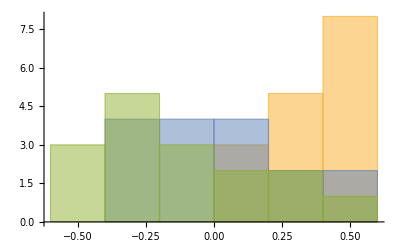

```mathematica
Histogram[Transpose@aList,4]
```